```mathematica
Clear[datdensity,colorfunc,rng,P1]
```

```mathematica
datFileLDOSlocation = "/HOTI_parent_data/LDOS/";
```

```mathematica
datfileOBCLDOSName="t0=1.0_t=1.0_m_0=-1.0_Delta=0.5_x_periodic=0_y_periodic=0_L=32";
```

```mathematica
datdensityOrig=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCLDOSName,".csv"]]];
```

```mathematica
(*colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]];*)
```

```mathematica
(*colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];*)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,0.8]];
```

```mathematica
nn=Dimensions[datdensityOrig][[1]]
```

1024

```mathematica
nnnn=Sqrt[nn]
```

32

```mathematica
datdensity=Table[{Mod[ii-1,nnnn]+1,Quotient[ii-1,nnnn]+1,datdensityOrig[[ii]]},{ii,1,nnnn^2}];
```

```mathematica
rngOld={0,Max[#]}&@datdensity[[All,3]]
```

{0,0.529871}

```mathematica
rng={0,0.54}
```

{0,0.54}

```mathematica
Dimensions[datdensity]
```

{1024,3}

```mathematica
FilteredData=Select[datdensity,#[[3]]>0.001&];
```

```mathematica
Dimensions[FilteredData]
```

{32,3}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.27"},{rng[[2]]-10^-6,"0.54"}}]
```

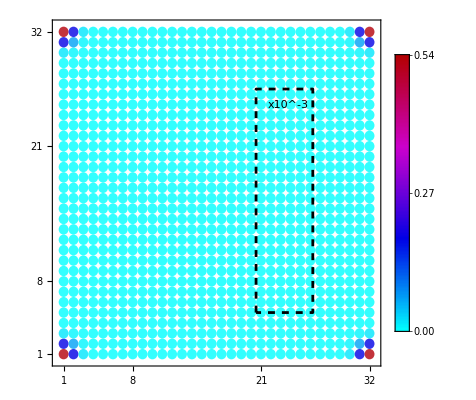

```mathematica
P2=Show[Graphics[{
PointSize[0.04],colorfunc[#[[3]],rng[[2]]],Disk[#[[1;;2]],0.5]
}&/@datdensity,

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,32},None},{{1,8,21,32},None}},BaseStyle-> 18,
PlotRange-> {{1nnnn},{1,nnnn}},

Epilog-> {Inset[P1,{23.5,14}],Inset["x10^-3",{23.75,25}]}],
ListPlot[{{20.5,5},{20.5,26.5},{26.25,26.5},{26.25,5},{20.5,5}},Joined-> True,PlotStyle-> {Black,Dashed}]
]
```

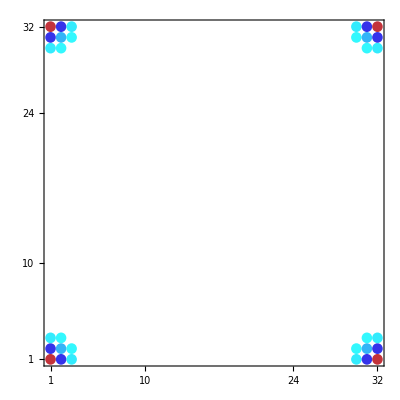

```mathematica
P2A=Show[Graphics[{
PointSize[0.04],colorfunc[#[[3]],rng[[2]]],Disk[#[[1;;2]],0.5]
}&/@FilteredData,
Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,10,24,32},None},{{1,10,24,32},None}},BaseStyle-> 40,
PlotRange-> {{1,nnnn},{1,nnnn}}
]]
```

```mathematica
Export["/home/archisman/Documents/GitHub/lattices-julia/HOTI_parent_data/LDOS/t0=1.0_t=1.0_m_0=-1.0_Delta=0.5_x_periodic=0_y_periodic=0_L=32.pdf",P2A]
```

/home/archisman/Documents/GitHub/lattices-julia/HOTI_parent_data/LDOS/t0=1.0_t=1.0_m_0=-1.0_Delta=0.5_x_periodic=0_y_periodic=0_L=32.pdf

```mathematica
Xaxis=Table[{{1,j},{nnnn,j}},{j,1,nnnn,1}];
```

```mathematica
Dimensions[Xaxis]
```

{32,2,2}

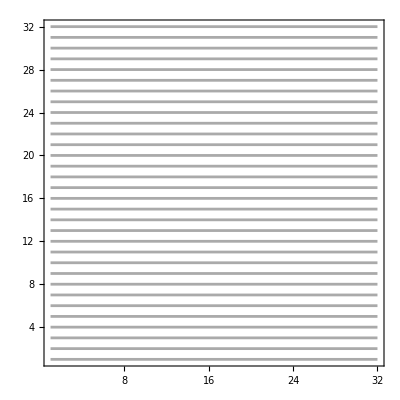

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,nnnn}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,nnnn},{1,nnnn}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,nnnn},None},{{1,8,21,nnnn},None}},BaseStyle-> 18]
```

```mathematica
Yaxis1=Table[{{j,1},{j,28}},{j,1,28,1}];
```

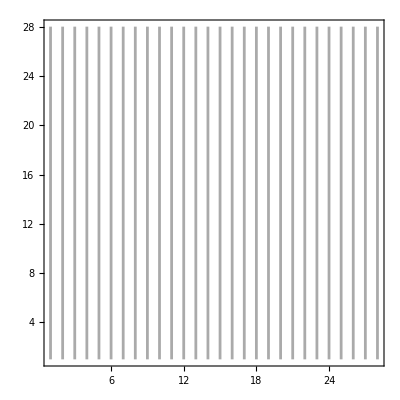

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,28}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,28},{1,28}},Frame-> True,Axes-> False,AspectRatio->1]
]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,8,21,28},None}},BaseStyle-> 18,
PlotRange-> {{1,28},{1,28}}
]]
```

-Graphics-

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

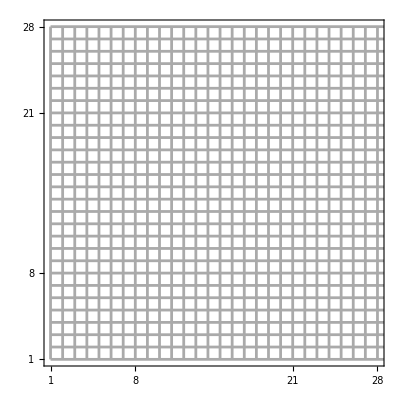

```mathematica
Show[P2B,P3,P4]
```

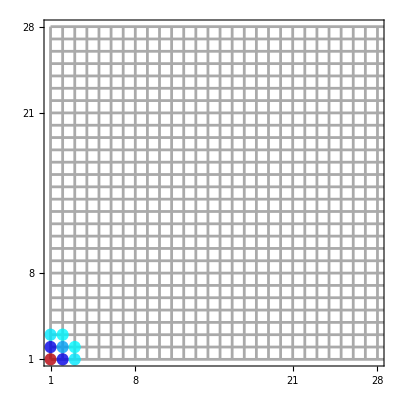

```mathematica
Show[P2B,P3,P4,P2A]
```

```mathematica
datFileEnergylocation="/HOTI_parent_data/energies/";
datfileOBCName="t0=1.0_t=1.0_m_0=-1.0_Delta=0.5_x_periodic=0_y_periodic=0_L=32";
```

```mathematica
StringJoin[datFileEnergylocation,datfileOBCName]
```

/HOTI_parent_data/energies/t0=1.0_t=1.0_m_0=-1.0_Delta=0.5_x_periodic=0_y_periodic=0_L=32

```mathematica
Clear[dataEnergyOBC]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataEnergyOBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".csv"]]];
```

```mathematica
Clear[Lattice];
```

```mathematica
Lattice=Table[{j,0},{j,1,Dimensions[dataEnergyOBC][[1]]/4}];
```

```mathematica
largestX = Dimensions[Lattice][[1]]
```

1024

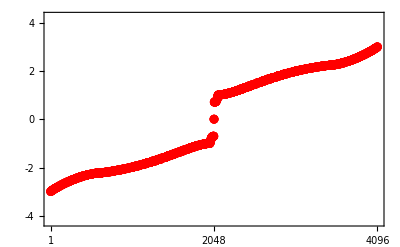

```mathematica
plt1=Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{0,4*largestX},{-4.25,4.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,2*largestX,4*largestX},None}},BaseStyle-> 18]

(**Plot[3,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Red}],
Plot[1.5,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{largestX,3}],Inset["PBC",{largestX,1.5}]}**)
]
```

```mathematica
largestX
```

1024

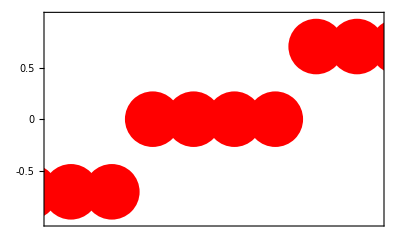

```mathematica
plt2=Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{2*largestX-3.5,2*largestX+4.5},{-1,1}},PlotStyle-> {Red,PointSize[0.1]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-0.5,0,0.5},None},{None,None}},BaseStyle-> 36]

(**Plot[3,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Red}],
Plot[1.5,{x,largestX-350,largestX-550},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{largestX,3}],Inset["PBC",{largestX,1.5}]}**)
]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".pdf"],plt1];
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,"zoom.pdf"],plt2];
```